```mathematica
@@@@@@@@@@@@@@@@@@@@@@@@@@@@@@@@@@@@@@@@@@@@@@@@@@@@@@@@@@@
	 check pictures
```

```mathematica
Remove["Global`*"]
time = 15;
n=131;
l=100;
next=15;
path="D:\\Igor\\24 evolution\\evolution\\PDF\\";
path=NotebookDirectory[]<>"data/my5/"
name = NotebookDirectory[]<>"ndd15tr.d";
fname=FileNameJoin[{ToString[name]}]
Data=ReadList[fname,{Number,Number,Number,Number,Number,Number,Number,Number,Number}];
zi = Data[[1]][[1]];
ws = Data[[1]][[2]];
ug=5;
(* - to m/s *)
Cu=ug;                
Cw= 1;
Ch=3000;
(* -/ to m/s *)
(* - to z/zi *)
Ch2=1/zi;
(* -/ to m/s *)

Do[eh[j]=Data[[j+1]][[2]],{j,1,n}];
Do[ep[j]=Data[[j+1]][[3]],{j,1,n}];
Do[w2[j]=Data[[j+1]][[4]],{j,1,n}];
Do[w3[j]=Data[[j+1]][[5]],{j,1,n}];
Do[u[j]=Data[[j+1]][[6]],{j,1,n}];
Do[v[j]=Data[[j+1]][[7]],{j,1,n}];
Do[vel[j]=Data[[j+1]][[8]],{j,1,n}];
Do[lambda[j]=Data[[j+1]][[9]],{j,1,n}];

Do[
z[j] =Data[[j+1]][[1]];
z[j] =z[j] *Ch2
,{j,1,n}];
Do[If[z[k]>1.2,If[z[k-1]<1.2,hcell=k]],{k,2,n}]
Do[If[z[k]>0.5,If[z[k-1]<0.5,hcentr=k]],{k,2,n}]
Do[
z[j] =Data[[j+1]][[1]]
,{j,1,n}];


hcentr
hcell
z[hcentr]
z[n]
zi
(*Do[If[z[k]>1.2,If[z[k-1]<1.2,hcell=k]],{k,2,n}];
Do[If[z[k]>0.5,If[z[k-1]<0.5,hcentr=k]],{k,2,n}];*)
```

/home/igor/Igor/evolution/xz/compare/data/my5/

/home/igor/Igor/evolution/xz/compare/ndd15tr.d

108

121

0.21566

0.99999

0.42019

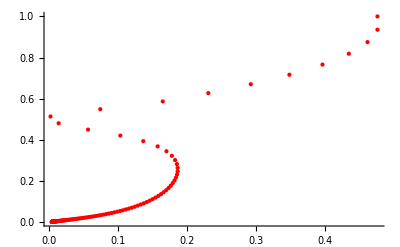

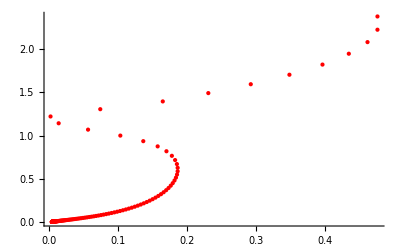
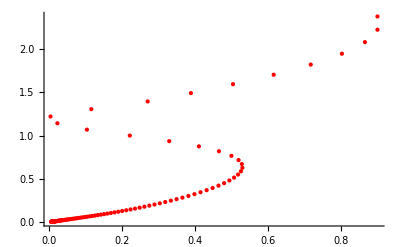

0.18388

0.42019

0.56052

0.358104

108

0.279581

1.52045

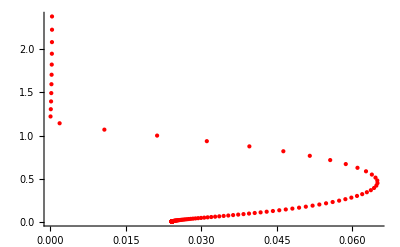

```mathematica
ListPlot[Table[{lambda[k],z[k]},{k,1,n}],PlotStyle->{Red,Thick}]
lambda[hcentr];
length = lambda[hcentr]*3000*5;

{1.5*ws,u[hcentr],6*ws};
Do[
lambda2[j]= 2*π/((1.9*1.6/eh[j])^(3/2)*ep[j])
,{j,1,n}];
Do[
lambda3[j]= 2*π/((1.9*1.6/(eh[j]+w2[j]/2))^(3/2)*ep[j])
,{j,1,n}];
{ListPlot[Table[{lambda2[k],z[k]/zi},{k,1,n}],PlotStyle->{Red,Thick}],ListPlot[Table[{lambda3[k],z[k]/zi},{k,1,n}],PlotStyle->{Red,Thick}]}
lambda2[hcentr]*3000*5;
lambda3[hcentr]*3000*5;
lambda2[hcentr]
zi
velCentr=(u[hcentr]^2+v[hcentr]^2)^0.5
ws
hcentr
xstar = ws/velCentr/zi*lambda2[hcentr]
xstar = ws/velCentr/zi
ListPlot[Table[{w2[k],z[k]/zi},{k,1,n}],PlotStyle->{Red,Thick}]
```

```mathematica
2.*api/(sqrt(1.9*1.6/eh(k))**3*ep(k))
```

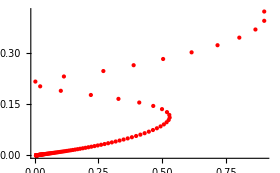

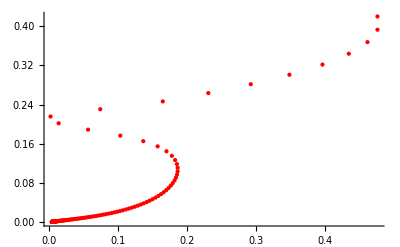

```mathematica
ListPlot[Table[{w2[k]/ws/ws,z[k]},{k,1,n}],PlotStyle->{Red,Thick}]
```

```mathematica
ListPlot[Table[{u[k]*Cu,z[k]},{k,1,n}],PlotStyle->{Red,Thick},PlotRange->{{0,5},{0,z[n]}}]
```

```mathematica
@@@@@@@@@@@@@@@@@@@@@@@@@@@@@@@@@@@@@@@@@@@@@@@@@@@@@@@@@@@
	 vector field
```

```mathematica
Remove["Global`*"]
time = 10;
n=130;
l=100;
next=15;
path=NotebookDirectory[]<>"data/my/"<>ToString[time]<>"/"
name = path<>"cell_tR.dat";
fname=FileNameJoin[{ToString[name]}]
Data=ReadList[fname,{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}];
zi = Data[[1]][[1]];
ws = Data[[1]][[2]];
ug=5;
(* - to m/s *)
Cu=ug;                
Cw= 1;
Ch=3000;
(* -/ to m/s *)
(* - to z/zi *)
Ch2=1/zi;
(* -/ to m/s *)
Do[
z[j] =Data[[2+2*l*(j-1)]][[2]];
z[j] =z[j] *Ch2;
,{j,1,n}]
Do[If[z[k]>1.2,If[z[k-1]<1.2,hcell=k]],{k,2,n}]
Do[If[z[k]>0.5,If[z[k-1]<0.5,hcentr=k]],{k,2,n}]
Do[
x[i] =Data[[1+i]][[1]]
,{i,1,2*l}]
Do[
u[j]=Data[[2+2*l*(j-1)]][[7]];
,{j,1,n}];
Do[
v[j]=Data[[2+2*l*(j-1)]][[8]];
,{j,1,n}];
Do[
vel[j]=Data[[2+2*l*(j-1)]][[11]];
,{j,1,n}];
Do[
slope[j]=Data[[2+2*l*(j-1)]][[11]];
,{j,1,n}];
Do[
Do[
uc[i,j]=Data[[1+i+2*l*(j-1)]][[5]],
{i,1,200}]
,{j,1,n}];
Do[
Do[
wc[i,j]=Data[[1+i+2*l*(j-1)]][[6]],
{i,1,200}]
,{j,1,n}];
tx=Table[{kl,x[kl]},{kl,1,2*l}];
tz=Table[{j,z[j]},{j,1,n}];
tu=Table[{j,u[j]},{j,1,n}];
tv=Table[{j,v[j]},{j,1,n}];
twc=Flatten[Table[{kl,j,wc[kl,j]},{kl,1,2*l},{j,1,hcell}],1];
tuc=Flatten[Table[{kl,j,uc[kl,j]},{kl,1,2*l},{j,1,hcell}],1];
velc=Sqrt[u[hcentr]^2+v[hcentr]^2];
fx=Interpolation[tx];
fz=Interpolation[tz];
fu=Interpolation[tu];
fv=Interpolation[tv];
fwc=Interpolation[twc];
fuc=Interpolation[tuc];
(*Do[eh[j]=Data[[j+1]][[2]],{j,1,n}];
Do[ep[j]=Data[[j+1]][[3]],{j,1,n}];
Do[w2[j]=Data[[j+1]][[4]],{j,1,n}];
Do[w3[j]=Data[[j+1]][[5]],{j,1,n}];
Do[vel[j]=Data[[j+1]][[8]],{j,1,n}];
Do[lambda[j]=Data[[j+1]][[9]],{j,1,n}];*)
hcell
hcentr
```

/home/igor/Igor/proga/fullDistribution/data/my/10/

/home/igor/Igor/proga/fullDistribution/data/my/10/cell_tR.dat

тот

96

83

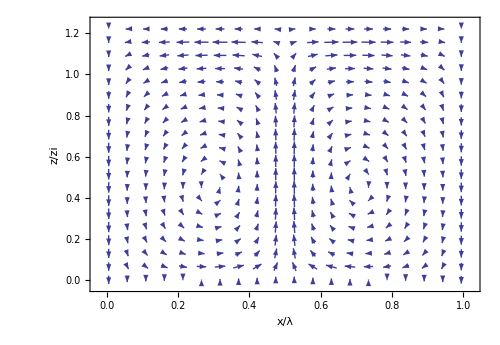

/home/igor/Igor/proga/fullDistribution/data/my/15/pictures/

/home/igor/Igor/proga/fullDistribution/data/my/15/pictures/

/home/igor/Igor/proga/fullDistribution/data/my/15/pictures/CELL.png

```mathematica
Clear[datavector]
(*datavector = Table[{fuc[kl,j],fwc[kl,j]},{kl,0,2*l-1,0.5},{j,1,hcell,0.5}];*)
datavector = Table[{{fx[kl],fz[j]},{fuc[kl,j],fwc[kl,j]}},{kl,1,2*l-1,0.5},{j,1,hcell,0.5}];
picture=ListVectorPlot[datavector,VectorPoints->{20,20},VectorScale->0.04,FrameLabel->{"x/λ","z/zi"},AspectRatio->0.69,ImageSize->500]
exportPictures=path<>"pictures/"
CreateDirectory[exportPictures]
Export[exportPictures<>"CELL.png",picture]
```

```mathematica
hcentr
hcell
Table[z[k]*zi,{k,1,n}]
Table[x[i],{i,1,2*l}];
Table[wc[i,2],{i,1,2*l}];
Table[wc[i,n],{i,1,2*l}];
```

108

121

{0.0001566,0.0001685,0.0001811,0.0001946,0.0002091,0.0002246,0.0002411,0.0002587,0.0002776,0.0002978,0.0003194,0.0003424,0.0003671,0.0003934,0.0004216,0.0004517,0.0004839,0.0005183,0.0005551,0.0005944,0.0006364,0.0006814,0.0007294,0.0007807,0.0008356,0.0008942,0.000957,0.001024,0.001096,0.001172,0.001254,0.001342,0.001435,0.001535,0.001642,0.001756,0.001879,0.002009,0.002149,0.002298,0.002458,0.002628,0.002811,0.003005,0.003214,0.003436,0.003674,0.003929,0.004201,0.004492,0.004802,0.005135,0.00549,0.005869,0.006275,0.006709,0.007173,0.007669,0.008198,0.008765,0.009371,0.01002,0.01071,0.01145,0.01224,0.01309,0.01399,0.01496,0.01599,0.01709,0.01827,0.01953,0.02088,0.02232,0.02386,0.02551,0.02727,0.02915,0.03116,0.03331,0.03561,0.03807,0.04069,0.0435,0.0465,0.04971,0.05314,0.05681,0.06072,0.06491,0.06939,0.07418,0.0793,0.08477,0.09061,0.09686,0.1036,0.1107,0.1183,0.1265,0.1352,0.1445,0.1545,0.1652,0.1766,0.1887,0.2017,0.2157,0.2305,0.2464,0.2634,0.2816,0.301,0.3218,0.344,0.3677,0.3931,0.4202,0.4492,0.4802,0.5133,0.5487,0.5865,0.627,0.6702,0.7164,0.7658,0.8187,0.8751,0.9355}

```mathematica
{ListPlot[Table[{u[k]*Cu,z[k]},{k,1,n}],PlotStyle->{Red,Thick}],ListPlot[Table[{v[k]*Cu,z[k]},{k,1,n}],PlotStyle->{Red,Thick}],ListPlot[Table[{vel[k]*Cu,z[k]},{k,1,n}],PlotStyle->{Red,Thick}]}
ListPlot[Table[{slope[k]*Cu,z[k]},{k,1,n}],PlotStyle->{Red,Thick}]
```

```mathematica
Table[ListPlot[Table[{uc[kl,k],z[k]},{k,1,n}],PlotStyle->{Red,Thick}],{kl,1,100,5}]
Table[ListPlot[Table[{wc[kl,k],z[k]},{k,1,n}],PlotStyle->{Red,Thick}],{kl,1,70,5}];
Table[ListPlot[Table[{wc[kl,k],z[k]},{k,1,n}],PlotStyle->{Red,Thick}],{kl,70,100,5}];
```

```mathematica
Remove["Global`*"]
time = 15;
n=131;
l=100;
next=15;
path="D:\\Igor\\24 evolution\\evolution\\PDF\\";
name = path<>"n15tr.dat";
fname=FileNameJoin[{ToString[name]}]
Data=ReadList[fname,{Number,Number,Number,Number,Number,Number,Number,Number,Number}];
zi = Data[[1]][[1]];
ws = Data[[1]][[2]];
ug=5;
(* - to m/s *)
Cu=ug;                
Cw= 1;
Ch=3000;
(* -/ to m/s *)
(* - to z/zi *)
Ch2=1/zi;
(* -/ to m/s *)
Do[
z[j] =Data[[j+1]][[1]];
,{j,1,n}];
Do[eh[j]=Data[[j+1]][[2]],{j,1,n}];
Do[ep[j]=Data[[j+1]][[3]],{j,1,n}];
Do[w2[j]=Data[[j+1]][[4]],{j,1,n}];
Do[w3[j]=Data[[j+1]][[5]],{j,1,n}];
Do[u[j]=Data[[j+1]][[6]],{j,1,n}];
Do[v[j]=Data[[j+1]][[7]],{j,1,n}];
Do[vel[j]=Data[[j+1]][[8]],{j,1,n}];
Do[
lambda[j]= 2*π/((1.9*1.6/eh[j])^(3/2)*ep[j])
,{j,1,n}];

Do[If[z[k]>1.2,If[z[k-1]<1.2,hcell=k]],{k,2,n}]
Do[If[z[k]>0.5,If[z[k-1]<0.5,hcentr=k]],{k,2,n}]




(*Do[If[z[k]>1.2,If[z[k-1]<1.2,hcell=k]],{k,2,n}];
Do[If[z[k]>0.5,If[z[k-1]<0.5,hcentr=k]],{k,2,n}];*)
```

D:\Igor\24 evolution\evolution\PDF\n15tr.dat

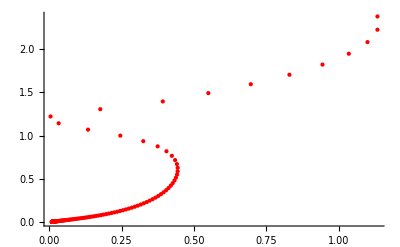

0.437612

551.641

```mathematica
ListPlot[Table[{lambda[k],z[k]},{k,1,n}],PlotStyle->{Red,Thick}]
lambda[hcentr]
lambda[hcentr]*3000*zi
```